```mathematica
f[x_,y_]:=Cos[x]Sin[x+y]
```

```mathematica
D[f[x,y],x]
```

Cos[x] Cos[x+y]-Sin[x] Sin[x+y]

```mathematica
D[f[x,y],y]
```

Cos[x] Cos[x+y]

```mathematica
fx[x_,y_]:=Cos[x] Cos[x+y]-Sin[x] Sin[x+y]
```

```mathematica
fy[x_,y_]:=Cos[x] Cos[x+y]
```

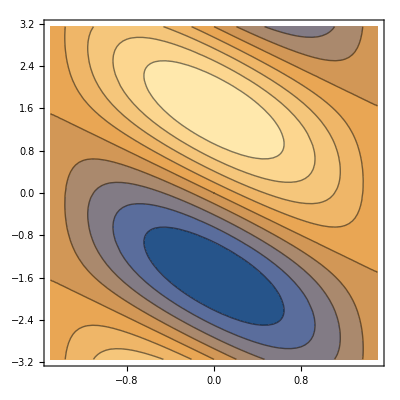

```mathematica
cp=ContourPlot[f[x,y],{x,-1.5,1.5},{y,-Pi,Pi}]
```

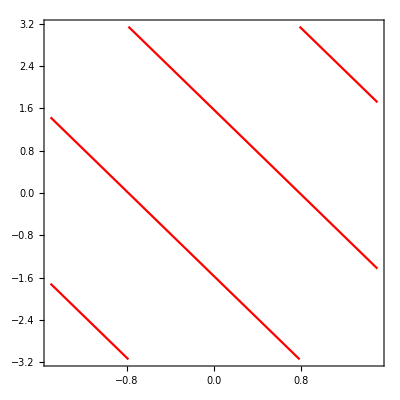

```mathematica
xpic=ContourPlot[fx[x,y]==0,{x,-1.5,1.5},{y,-Pi,Pi},ContourStyle->Red]
```

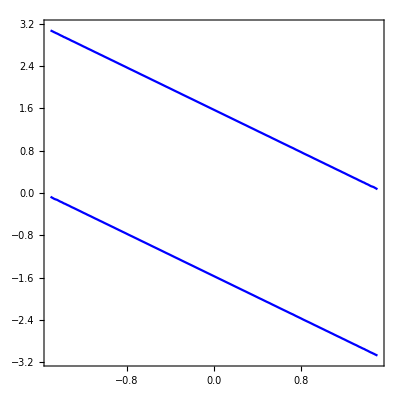

```mathematica
ypic=ContourPlot[fy[x,y]==0,{x,-1.5,1.5},{y,-Pi,Pi},ContourStyle->Blue]
```

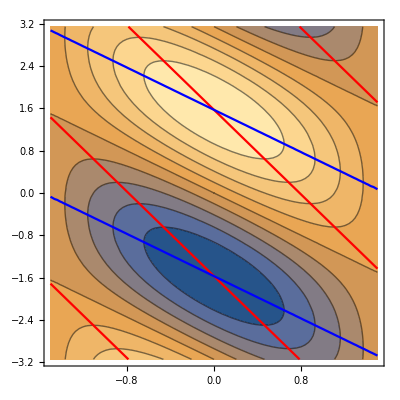

```mathematica
Show[cp,xpic,ypic]
```

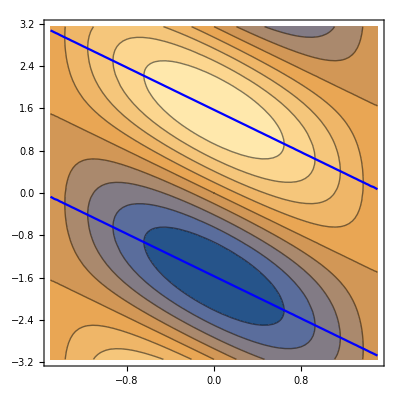

```mathematica
Show[cp,ypic]
```